```mathematica
Quit[]
```

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(-1/2),MZp->2*MD2,MD2->MD1*(1+10^(-3/10)),MD1->100};
DMabundance[ModelParam]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (20.).

NDSolve::mxst: Maximum number of 10000 steps reached at the point x == 25.418542281832554187.

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

812645.

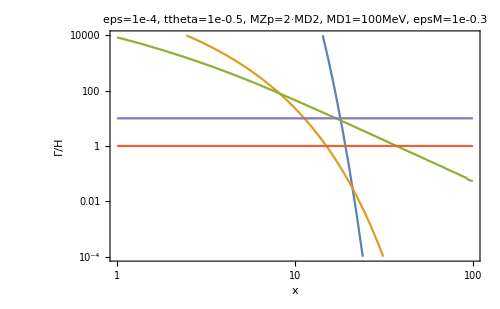

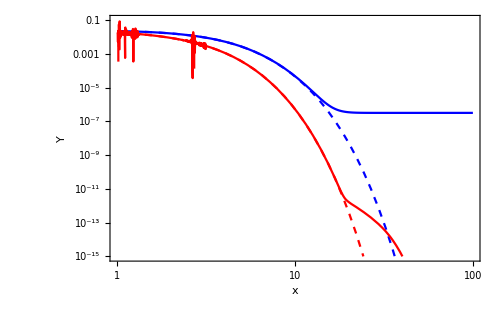

```mathematica
LogLogPlot[{MedAnnRate[x]/(neqDM[x]*H[MD1/x])/.ModelParam,CoscatRate[x]/(neqDM[x]*H[MD1/x])/.ModelParam,DMScatRate[x]/(neqDM[x]*H[MD1/x])/.ModelParam,1,10},{x,1,100},Frame->True,PlotRange->{All,{10^-4,10^4}},FrameLabel->{"x","Γ/H"},PlotLabel->"eps=1e-4, ttheta=1e-0.5, MZp=2·MD2, MD1=100MeV, epsM=1e-0.3",ImageSize->500]
LogLogPlot[{Ydm[x],YeqDM[x],Ymed[x],YeqMed[x]},{x,1,100},PlotStyle->{Blue,{Blue,Dashed},Red,{Red,Dashed}},Frame->True,PlotRange->{All,{10^-15,10^-1}},FrameLabel->{"x","Y"},ImageSize->500]
```

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
```

```mathematica
ModelParam={aX->1,epsilon->10^-5,ttheta->10^(-2),MD2->MD1*(1+10^(0)),MD1->100};
```

ReplaceRepeated::reps: {Join[Relations,SMMasses,ModelParam]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

-Graphics-

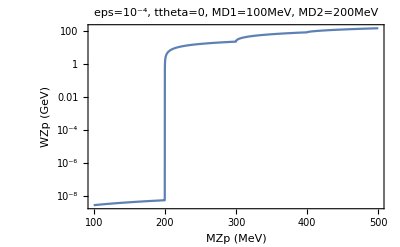

```mathematica
Wzp=(EE^2*Sqrt[(-4*ME^2 + MZp^2)]*(cw^4*sa^2 - 
       2*cw^2*sa*sw*(ca*eta + sa*sw) + 5*sw^2*(ca*eta + sa*sw)^2))/(96*cw^2*Pi*sw^2) +ca^2 ctheta^4 eta^2 gX^2 Sqrt[-4 MD2^2+MZp^2] (2 MD2^2+MZp^2)/(12 chi^2 MZp^2 π)HeavisideTheta[MZp-2*MD2]+ca^2 stheta^4 eta^2 gX^2 Sqrt[-4 MD1^2+MZp^2] (2 MD1^2+MZp^2)/(12 chi^2 MZp^2 π)HeavisideTheta[MZp-2*MD1]-(ca^2*ctheta^2*eta^2*gX^2*Sqrt[(-(MD1-MD2)^2+MZp^2)*(-(MD1+MD2)^2+MZp^2)]*(MD1^4+MD2^4-6*MD1*MD2*MZp^2+MD2^2*MZp^2-2*MZp^4+MD1^2*(-2*MD2^2+MZp^2))*stheta^2)/(12*chi^2*MZp^5*Pi)HeavisideTheta[MZp-(MD1+MD2)]//.Join[Relations,SMMasses,ModelParam];
LogPlot[Wzp/.MZp->Mzp,{Mzp,100,500},Frame->True,FrameLabel->{"MZp (MeV)","WZp (GeV)"},LabelStyle->Larger,PlotStyle->Large, PlotLabel->"eps=10^-5, ttheta=-2, MD1=100MeV, MD2=200MeV"]
```

$Aborted

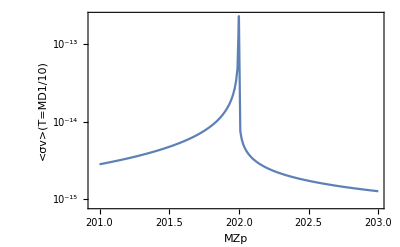

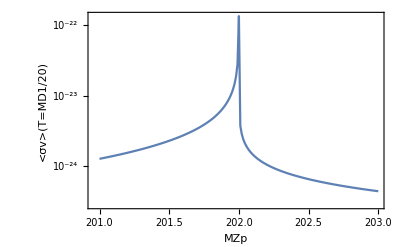

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
ModelParam={aX->1,epsilon->10^-5,ttheta->10^(-2),MZp->Mzp,MD2->MD1*(1+10^(-2)),MD1->100};
ListLogPlot[Table[{Mzp,CalcGaScat[ModelParam,10,2]},{Mzp,201,203,1*10^-2}],Joined->True,Frame->True,FrameLabel->{"MZp","<σv>(T=MD1/10)"},LabelStyle->Larger]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.2367318491656068489}. NIntegrate obtained 2.3137869881710994145×10^-68 and 3.0627651433027688347×10^-78 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.2367318491656068489}. NIntegrate obtained 4.6096750359311863911×10^-69 and 8.3180732316128683374×10^-79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.2367318491656068489}. NIntegrate obtained 8.1725495553257343989×10^-70 and 2.3487622099565431952×10^-79 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.127767334976963958}. NIntegrate obtained 1.352449268889682148×10^-68 and 1.6133575310746269527×10^-78 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.127767334976963958}. NIntegrate obtained 2.5516432112815064585×10^-69 and 4.4006814311171113238×10^-79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.127767334976963958}. NIntegrate obtained 4.2506346944254434505×10^-70 and 1.0482388451252399357×10^-79 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

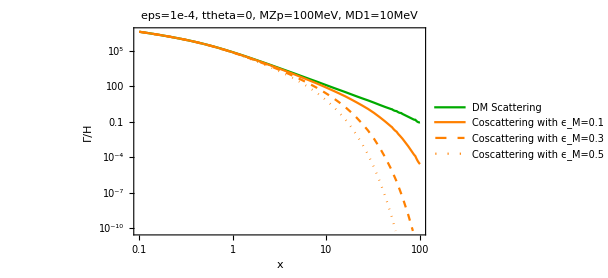

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
xval=Round[10^Range[Log10[10^-1],Log10[100],0.05]*10^5]*10^-5;
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->100,MD2->MD1*(1+1*10^-1),MD1->10};
Data1=AveragedXsec[ModelParam,1,xval];
Rate1[x_]:=If[x<Data1[[-1,1]],Exp[Interpolation[Log[Data1],Log[x],InterpolationOrder->1]],0];
Data31=AveragedXsec[ModelParam,3,xval];
Rate31[x_]:=If[x<Data31[[-1,1]],Exp[Interpolation[Log[Data31],Log[x],InterpolationOrder->1]],0];
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->100,MD2->MD1*(1+3*10^-1),MD1->10};
Data32=AveragedXsec[ModelParam,3,xval];
Rate32[x_]:=If[x<Data32[[-1,1]],Exp[Interpolation[Log[Data32],Log[x],InterpolationOrder->1]],0];
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->100,MD2->MD1*(1+5*10^-1),MD1->10};
Data33=AveragedXsec[ModelParam,3,xval];
Rate33[x_]:=If[x<Data33[[-1,1]],Exp[Interpolation[Log[Data33],Log[x],InterpolationOrder->1]],0];
LogLogPlot[{Rate1[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate31[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate32[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate33[x]/(neqDM[x]*H[MD1/x])/.ModelParam},{x,xval[[1]],xval[[-1]]},Frame->True,FrameLabel->{"x","Γ/H"},PlotLabel->Style ["eps=1e-4, ttheta=0, MZp=100MeV, MD1=10MeV",FontSize->15],LabelStyle->Larger,ImageSize->450,PlotStyle->{Darker[Green],Orange,{Orange,Dashed},{Orange,Dotted}},PlotLegends->{"DM Scattering","Coscattering with ϵ_M=0.1","Coscattering with ϵ_M=0.3","Coscattering with ϵ_M=0.5"}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 4.9338326605460809513×10^-54 and 1.236856336443056643×10^-59 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 1.863397527527484459×10^-54 and 3.6137575975006719639×10^-60 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 6.9309798488843062736×10^-55 and 9.2786265924102209828×10^-61 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {17645.588923927253942}. NIntegrate obtained 1.7487651379527299249×10^-53 and 1.8075365340784446415×10^-63 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.8286083168172425977}. NIntegrate obtained 1.2989053479729394297×10^-61 and 1.3743449919735374751×10^-71 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.8286083168172425977}. NIntegrate obtained 5.2709675091530952676×10^-62 and 7.9194786633501680868×10^-72 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 4.9333459392876151851×10^-58 and 1.2373672165269719453×10^-63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 1.8631877603113460133×10^-58 and 3.6153665126460104934×10^-64 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 6.9300908062430602455×10^-59 and 9.2821972844001555151×10^-65 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {17645.588923927253942}. NIntegrate obtained 1.7484154471056737322×10^-57 and 1.80718951360015668×10^-67 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.8286083168172425977}. NIntegrate obtained 1.7773859577663003457×10^-64 and 2.6173397986435962864×10^-74 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.8286083168172425977}. NIntegrate obtained 7.5241300587537571272×10^-65 and 1.8601373612239777592×10^-74 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 4.9333458906196563553×10^-62 and 1.2373672676291058084×10^-67 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 1.8631877393365829252×10^-62 and 3.6153666735574735555×10^-68 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 6.9300907173477890945×10^-63 and 9.2821976414844922945×10^-69 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {17645.588923927253942}. NIntegrate obtained 1.7484154121418513659×10^-61 and 1.8071750459737216379×10^-71 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.8286083168172425977}. NIntegrate obtained 1.2986455889656803355×10^-69 and 1.3733886528859241734×10^-79 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.8286083168172425977}. NIntegrate obtained 5.2699134052355521887×10^-70 and 7.9111492165480690298×10^-80 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

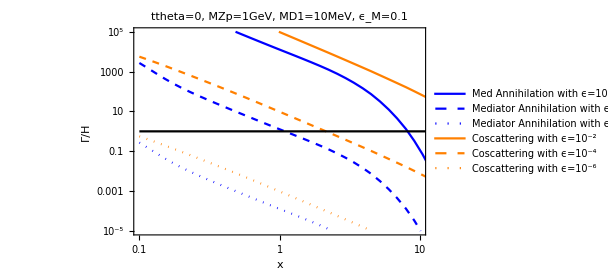

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
xval=Round[10^Range[Log10[10^-1],Log10[100],0.05]*10^5]*10^-5;
ModelParam={aX->1,epsilon->10^-2,ttheta->10^(0),MZp->1000,MD2->MD1(1+10^-1),MD1->10};
Data21=AveragedXsec[ModelParam,2,xval];
Rate21[x_]:=If[x<Data21[[-1,1]],Exp[Interpolation[Log[Data21],Log[x],InterpolationOrder->1]],0];
Data31=AveragedXsec[ModelParam,3,xval];
Rate31[x_]:=If[x<Data31[[-1,1]],Exp[Interpolation[Log[Data31],Log[x],InterpolationOrder->1]],0];
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->1000,MD2->MD1(1+10^-1),MD1->10};
Data22=AveragedXsec[ModelParam,2,xval];
Rate22[x_]:=If[x<Data22[[-1,1]],Exp[Interpolation[Log[Data22],Log[x],InterpolationOrder->1]],0];
Data32=AveragedXsec[ModelParam,3,xval];
Rate32[x_]:=If[x<Data32[[-1,1]],Exp[Interpolation[Log[Data32],Log[x],InterpolationOrder->1]],0];
ModelParam={aX->1,epsilon->10^-6,ttheta->10^(0),MZp->1000,MD2->MD1(1+10^-1),MD1->10};
Data23=AveragedXsec[ModelParam,2,xval];
Rate23[x_]:=If[x<Data23[[-1,1]],Exp[Interpolation[Log[Data23],Log[x],InterpolationOrder->1]],0];
Data33=AveragedXsec[ModelParam,3,xval];
Rate33[x_]:=If[x<Data33[[-1,1]],Exp[Interpolation[Log[Data33],Log[x],InterpolationOrder->1]],0];
LogLogPlot[{Rate21[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate22[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate23[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate31[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate32[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate33[x]/(neqDM[x]*H[MD1/x])/.ModelParam,1},{x,xval[[1]],xval[[-1]]},Frame->True,FrameLabel->{"x","Γ/H"},PlotLabel->Style ["ttheta=0, MZp=1GeV, MD1=10MeV, ϵ_M=0.1",FontSize->15],LabelStyle->Larger,ImageSize->450,PlotStyle->{Blue,{Blue,Dashed},{Blue,Dotted},Orange,{Orange,Dashed},{Orange,Dotted},Black},PlotLegends->{"Med Annihilation with ϵ=10^-2","Mediator Annihilation with ϵ=10^-4","Mediator Annihilation with ϵ=10^-6","Coscattering with ϵ=10^-2","Coscattering with ϵ=10^-4","Coscattering with ϵ=10^-6"},PlotRange->{{0.1,10},{10^-5,10^5}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 4.9333459392876151851×10^-58 and 1.2373672165269719453×10^-63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 1.8631877603113460133×10^-58 and 3.6153665126460104934×10^-64 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 6.9300908062430602455×10^-59 and 9.2821972844001555151×10^-65 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {17645.588923927253942}. NIntegrate obtained 1.7484154471056737322×10^-57 and 1.80718951360015668×10^-67 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.8286083168172425977}. NIntegrate obtained 1.7773859577663003457×10^-64 and 2.6173397986435962864×10^-74 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.8286083168172425977}. NIntegrate obtained 7.5241300587537571272×10^-65 and 1.8601373612239703266×10^-74 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {570.12886440393050432}. NIntegrate obtained 1.4924221773850879506×10^-58 and 3.2724259835258666813×10^-66 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {570.12886440393050432}. NIntegrate obtained 5.6363256024004608935×10^-59 and 7.6585736715040279249×10^-67 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {570.12886440393050432}. NIntegrate obtained 2.0963388568602303903×10^-59 and 9.8500115983158716877×10^-68 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.1034617086027443453}. NIntegrate obtained 1.7453582959204680507×10^-65 and 2.9625686269846658739×10^-75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.1034617086027443453}. NIntegrate obtained 6.8391761561127782786×10^-66 and 1.5786562733854974109×10^-75 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.1034617086027443453}. NIntegrate obtained 2.6100176750555622967×10^-66 and 1.0277912466356468841×10^-75 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.000000018691176902094655385527827603198197013043784500477149750126313}. NIntegrate obtained 3.574653322579327674237851159649804005578060586732090279343130151664434×10^-335 and 8.871621881988531019848282172921264637226168339266844931137026584683627×10^-352 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.000000018691176902094655385527827603198197013043784500477149750126313}. NIntegrate obtained 3.93860182487947742892848463063927188024557431785723334367067751318331×10^-368 and 1.055249467972298708484517808529023569118443140651896514113579966494334×10^-384 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.000000018691176902094655385527827603198197013043784500477149750126313}. NIntegrate obtained 4.249639172859264767549232569165309674401569038757321415438864033579053×10^-405 and 1.586047286795918566351259106872067264800763044091146424920826256790851×10^-421 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.000000000088664262210116873433903027643038104039205377349228576700127}. NIntegrate obtained 5.14923479230244786377828262414075649923161315230118822467838504978517×10^-339 and 2.193460654931683116110625074790066029577521961859458966849781620812394×10^-354 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.000000000088664262210116873433903027643038104039205377349228576700127}. NIntegrate obtained 4.73679551861419069643630061643378139350538981765052096250176422783017×10^-372 and 2.102690711159169291933009698461886880919132913208514281008339774695992×10^-387 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.000000000088664262210116873433903027643038104039205377349228576700127}. NIntegrate obtained 4.203420435951874829258904579375428659169293000010761238070122388632709×10^-409 and 2.285248571411798112483428960117427179126379778860706357119392775327938×10^-424 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

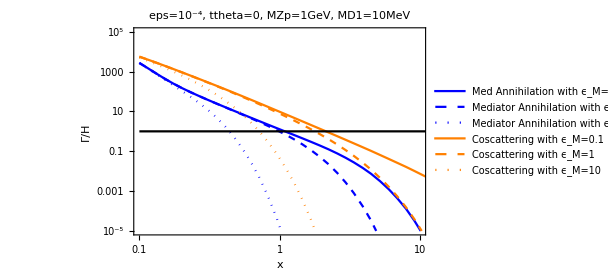

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
xval=Round[10^Range[Log10[10^-1],Log10[100],0.05]*10^5]*10^-5;
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->1000,MD2->MD1(1+10^-1),MD1->10};
Data21=AveragedXsec[ModelParam,2,xval];
Rate21[x_]:=If[x<Data21[[-1,1]],Exp[Interpolation[Log[Data21],Log[x],InterpolationOrder->1]],0];
Data31=AveragedXsec[ModelParam,3,xval];
Rate31[x_]:=If[x<Data31[[-1,1]],Exp[Interpolation[Log[Data31],Log[x],InterpolationOrder->1]],0];
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->1000,MD2->MD1(1+10^0),MD1->10};
Data22=AveragedXsec[ModelParam,2,xval];
Rate22[x_]:=If[x<Data22[[-1,1]],Exp[Interpolation[Log[Data22],Log[x],InterpolationOrder->1]],0];
Data32=AveragedXsec[ModelParam,3,xval];
Rate32[x_]:=If[x<Data32[[-1,1]],Exp[Interpolation[Log[Data32],Log[x],InterpolationOrder->1]],0];
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->1000,MD2->MD1(1+10^1),MD1->10};
Data23=AveragedXsec[ModelParam,2,xval];
Rate23[x_]:=If[x<Data23[[-1,1]],Exp[Interpolation[Log[Data23],Log[x],InterpolationOrder->1]],0];
Data33=AveragedXsec[ModelParam,3,xval];
Rate33[x_]:=If[x<Data33[[-1,1]],Exp[Interpolation[Log[Data33],Log[x],InterpolationOrder->1]],0];
LogLogPlot[{Rate21[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate22[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate23[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate31[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate32[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate33[x]/(neqDM[x]*H[MD1/x])/.ModelParam,1},{x,xval[[1]],xval[[-1]]},Frame->True,FrameLabel->{"x","Γ/H"},PlotLabel->Style ["eps=10^-4, ttheta=0, MZp=1GeV, MD1=10MeV",FontSize->15],LabelStyle->Larger,ImageSize->450,PlotStyle->{Blue,{Blue,Dashed},{Blue,Dotted},Orange,{Orange,Dashed},{Orange,Dotted},Black},PlotLegends->{"Med Annihilation with ϵ_M=0.1","Mediator Annihilation with ϵ_M=1","Mediator Annihilation with ϵ_M=10","Coscattering with ϵ_M=0.1","Coscattering with ϵ_M=1","Coscattering with ϵ_M=10"},PlotRange->{{0.1,10},{10^-5,10^5}}]
```

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
xval=Round[10^Range[Log10[10^-1],Log10[100],0.05]*10^5]*10^-5;
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->1000,MD2->MD1(1+10^-1),MD1->10};
Data11=AveragedXsec[ModelParam,2,xval];
Rate11[x_]:=If[x<Data11[[-1,1]],Exp[Interpolation[Log[Data11],Log[x],InterpolationOrder->1]],0];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 4.9333459392876151851×10^-58 and 1.2373672165269719453×10^-63 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 1.8631877603113460133×10^-58 and 3.6153665126460104934×10^-64 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1985.7652954429795174}. NIntegrate obtained 6.9300908062430602455×10^-59 and 9.2821972844001555151×10^-65 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Rate11[1]/(neqDM[1]*H[MD1/1])/.ModelParam
```

1.268768484651864942

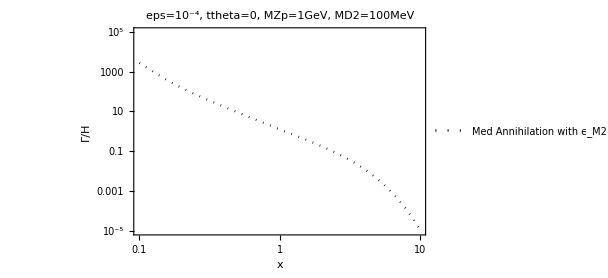

```mathematica
LogLogPlot[{Rate11[x]/(neqDM[x]*H[MD1/x])/.ModelParam},{x,xval[[1]],xval[[-1]]},Frame->True,FrameLabel->{"x","Γ/H"},PlotLabel->Style ["eps=10^-4, ttheta=0, MZp=1GeV, MD2=100MeV",FontSize->15],LabelStyle->Larger,ImageSize->450,PlotStyle->{Blue,{Blue,Dashed},{Blue,Dotted},Orange,{Orange,Dashed},{Orange,Dotted},Black},PlotLegends->{"Med Annihilation with ϵ_M2=0.01","Mediator Annihilation with ϵ_M2=0.1","Mediator Annihilation with ϵ_M2=0.9","Coscattering with ϵ_M2=0.01","Coscattering with ϵ_M2=0.1","Coscattering with ϵ_M2=0.9"},PlotRange->{{0.1,10},{10^-5,10^5}}]
```

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
xval=Round[10^Range[Log10[10^-1],Log10[100],0.05]*10^5]*10^-5;
ModelParam1={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->1000,MD1->MD2(1+10^-1),MD2->100};
Data21=AveragedXsec[ModelParam1,2,xval];
Rate21[x_]:=If[x<Data21[[-1,1]],Exp[Interpolation[Log[Data21],Log[x],InterpolationOrder->1]],0];
```

```mathematica
Rate21[1]/(neqDM[1]*H[MD1/1])//.ModelParam1
```

6.38492473805578253×10^6

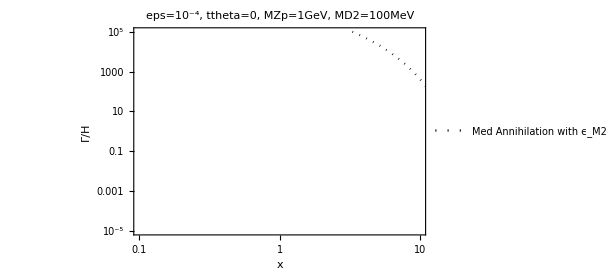

```mathematica
LogLogPlot[{Rate21[x]/(neqDM[x]*H[MD1/x])//.ModelParam1},{x,xval[[1]],xval[[-1]]},Frame->True,FrameLabel->{"x","Γ/H"},PlotLabel->Style ["eps=10^-4, ttheta=0, MZp=1GeV, MD2=100MeV",FontSize->15],LabelStyle->Larger,ImageSize->450,PlotStyle->{Blue,{Blue,Dashed},{Blue,Dotted},Orange,{Orange,Dashed},{Orange,Dotted},Black},PlotLegends->{"Med Annihilation with ϵ_M2=0.01","Mediator Annihilation with ϵ_M2=0.1","Mediator Annihilation with ϵ_M2=0.9","Coscattering with ϵ_M2=0.01","Coscattering with ϵ_M2=0.1","Coscattering with ϵ_M2=0.9"},PlotRange->{{0.1,10},{10^-5,10^5}}]
```

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
xval=Round[10^Range[Log10[10^-1],Log10[100],0.05]*10^5]*10^-5;
ModelParam1={aX->1,epsilon->10^-2,ttheta->10^(0),MZp->1000,MD2->100,MD1->MD2(1-10^-2)};
Data21=AveragedXsec[ModelParam1,2,xval];
Rate21[x_]:=If[x<Data21[[-1,1]],Exp[Interpolation[Log[Data21],Log[x],InterpolationOrder->1]],0];
Data31=AveragedXsec[ModelParam1,3,xval];
Rate31[x_]:=If[x<Data31[[-1,1]],Exp[Interpolation[Log[Data31],Log[x],InterpolationOrder->1]],0];
ModelParam2={aX->1,epsilon->10^-2,ttheta->10^(0),MZp->1000,MD2->100,MD1->MD2(1-10^-1)};
Data22=AveragedXsec[ModelParam2,2,xval];
Rate22[x_]:=If[x<Data22[[-1,1]],Exp[Interpolation[Log[Data22],Log[x],InterpolationOrder->1]],0];
Data32=AveragedXsec[ModelParam2,3,xval];
Rate32[x_]:=If[x<Data32[[-1,1]],Exp[Interpolation[Log[Data32],Log[x],InterpolationOrder->1]],0];
ModelParam3={aX->1,epsilon->10^-2,ttheta->10^(0),MZp->1000,MD2->100,MD1->MD2(1-9 10^-1)};
Data23=AveragedXsec[ModelParam3,2,xval];
Rate23[x_]:=If[x<Data23[[-1,1]],Exp[Interpolation[Log[Data23],Log[x],InterpolationOrder->1]],0];
Data33=AveragedXsec[ModelParam3,3,xval];
```

```mathematica
Rate33[x_]:=If[x<Data33[[-1,1]],Exp[Interpolation[Log[Data33],Log[x],InterpolationOrder->1]],0];
```

```mathematica
{Rate21[1],Rate22[2],Rate23[1],Rate33[1]}
```

{0.027565414727062429992,0.00001394969106545574481,5.9918318650049080057×10^-15,6.831402343550193638×10^-12}

```mathematica
AveragedXsec[{aX->1,epsilon->10^-4,ttheta->10^(0),MZp->1000,MD2->100,MD1->99},2,{1/10}]
```

{{1/10,1.2275425103144115217}}

```mathematica
AveragedXsec[{aX->1,epsilon->10^-4,ttheta->10^(0),MZp->1000,MD2->100,MD1->98},2,{1/10}]
```

{{1/10,1.1846120051853059058}}

```mathematica
WZp/.Relations/.{aX->1,epsilon->10^-4,ttheta->10^(0),MZp->1000,MD2->100,MD1->99}
```

(34 √6 ca^2 ctheta^4 eta^2 gX^2)/(chi^2 π)+(67306765693167 √97989801 ca^2 ctheta^2 eta^2 gX^2 stheta^2)/(4000000000000000 chi^2 π)+(509801 √240199 ca^2 eta^2 gX^2 stheta^4)/(3000000 chi^2 π)+(EE^2 √(1000000-4 ME^2) (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2))/(96 cw^2 π sw^2)

ReplaceRepeated::reps: {ModelParam} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

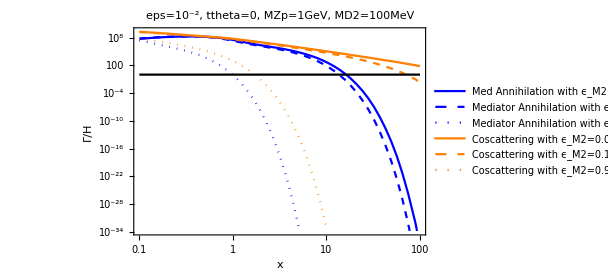

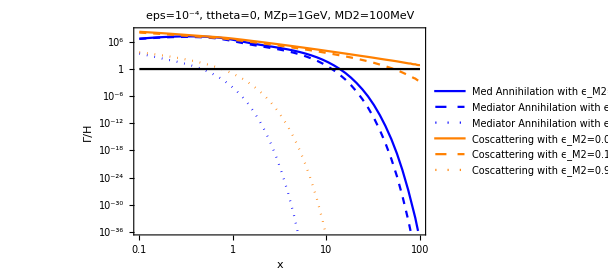

```mathematica
Rate33[x_]:=If[x<Data33[[-1,1]],Exp[Interpolation[Log[Data33],Log[x],InterpolationOrder->1]],0];
LogLogPlot[{Rate21[x]/(neqDM[x]*H[MD1/x])//.ModelParam1/.ModelParam-> ModelParam1,Rate22[x]/(neqDM[x]*H[MD1/x])//.ModelParam2/.ModelParam-> ModelParam2,Rate23[x]/(neqDM[x]*H[MD1/x])//.ModelParam3/.ModelParam-> ModelParam3,Rate31[x]/(neqDM[x]*H[MD1/x])//.ModelParam1/.ModelParam-> ModelParam1,Rate32[x]/(neqDM[x]*H[MD1/x])//.ModelParam2/.ModelParam-> ModelParam2,Rate33[x]/(neqDM[x]*H[MD1/x])//.ModelParam3/.ModelParam-> ModelParam3,1},{x,xval[[1]],xval[[-1]]},Frame->True,FrameLabel->{"x","Γ/H"},PlotLabel->Style ["eps=10^-2, ttheta=0, MZp=1GeV, MD2=100MeV",FontSize->15],LabelStyle->Larger,ImageSize->450,PlotStyle->{Blue,{Blue,Dashed},{Blue,Dotted},Orange,{Orange,Dashed},{Orange,Dotted},Black},PlotLegends->{"Med Annihilation with ϵ_M2=0.01","Mediator Annihilation with ϵ_M2=0.1","Mediator Annihilation with ϵ_M2=0.9","Coscattering with ϵ_M2=0.01","Coscattering with ϵ_M2=0.1","Coscattering with ϵ_M2=0.9"}(*,PlotRange->{{0.1,10},{10^-5,10^5}}*)]
```

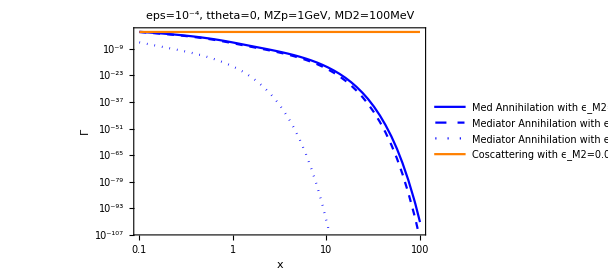

```mathematica
LogLogPlot[{Rate21[x]//.ModelParam1,Rate22[x]//.ModelParam2,Rate23[x]//.ModelParam3,1},{x,xval[[1]],xval[[-1]]},Frame->True,FrameLabel->{"x","Γ"},PlotLabel->Style ["eps=10^-4, ttheta=0, MZp=1GeV, MD2=100MeV",FontSize->15],LabelStyle->Larger,ImageSize->450,PlotStyle->{Blue,{Blue,Dashed},{Blue,Dotted},Orange,{Orange,Dashed},{Orange,Dotted},Black},PlotLegends->{"Med Annihilation with ϵ_M2=0.01","Mediator Annihilation with ϵ_M2=0.1","Mediator Annihilation with ϵ_M2=0.9","Coscattering with ϵ_M2=0.01","Coscattering with ϵ_M2=0.1","Coscattering with ϵ_M2=0.9"}(*,PlotRange->{{0.1,10},{10^-5,10^5}}*)]
```

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
xval=Round[10^Range[Log10[10^-1],Log10[100],0.05]*10^5]*10^-5;
ModelParam1={aX->1,epsilon->10^-2,ttheta->10^(0),MZp->1000,MD2->100,MD1->MD2(1-0.9)};
Data21=AveragedXsec[ModelParam1,2,xval];
Rate21[x_]:=If[x<Data21[[-1,1]],Exp[Interpolation[Log[Data21],Log[x],InterpolationOrder->1]],0];
Data31=AveragedXsec[ModelParam1,3,xval];
Rate31[x_]:=If[x<Data31[[-1,1]],Exp[Interpolation[Log[Data31],Log[x],InterpolationOrder->1]],0];
```

NIntegrate::precw: The precision of the argument function ((1.878407812373397334514721265×10^-45 «5» BesselK[1.,«19» √y])/((-40000.+40000. y) («1») (6.91798081536×10^19+8.31744×10^9 («1»)+1.6×10^9 y^2))) is less than WorkingPrecision (20.).

NIntegrate::precw: The precision of the argument function ((1.878407812373397334514721265×10^-45 «5» BesselK[1.,2.244 √y])/((-40000.+40000. y) («1») (6.91798081536×10^19+8.31744×10^9 («1»)+1.6×10^9 y^2))) is less than WorkingPrecision (20.).

NIntegrate::precw: The precision of the argument function ((1.878407812373397334514721265×10^-45 «5» BesselK[1.,«19» √y])/((-40000.+40000. y) («1») (6.91798081536×10^19+8.31744×10^9 («1»)+1.6×10^9 y^2))) is less than WorkingPrecision (20.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.000000018691176902094655385527827603198197013043784500477149750126313}. NIntegrate obtained 8.54817530996563629581934470314332569388359259589807310270156062334033×10^-337 and 2.496633970840164563278247172396184081266594259716771044483667007247929×10^-353 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.000000018691176902094655385527827603198197013043784500477149750126313}. NIntegrate obtained 2.071779244278372707062576677250658981862414991931299255919392345339644×10^-370 and 5.765711797112162709158697029122405414613094010500234324963005058371096×10^-387 for the integral and error estimates.

General::munfl: 0.1 2.9971879525104035935×10^-320 is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.000000018691176902094655385527827603198197013043784500477149750126313}. NIntegrate obtained 4.086747472970768577346239808439064034920846482000937465648607654935327×10^-408 and 1.593815397897421321701127021981628104747355389357882750489003762624649×10^-424 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::munfl: 0.1 5.2692436907564043027×10^-358 is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::precw: The precision of the argument function ((1.416004857220969046170568618002×10^-49 √y (-«18»+«1») BesselK[1.,1.00511 √y] («1»))/(100.-10102.461121 y)^2) is less than WorkingPrecision (20.).

NIntegrate::precw: The precision of the argument function ((1.416004857220969046170568618002×10^-49 √y (-«18»+(«1»)/y) BesselK[1.,1.12773 √y] («1»))/(100.-10102.461121 y)^2) is less than WorkingPrecision (20.).

NIntegrate::precw: The precision of the argument function ((1.416004857220969046170568618002×10^-49 √y (-«18»+«1») BesselK[1.,1.26533 √y] («1»))/(100.-10102.461121 y)^2) is less than WorkingPrecision (20.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.000000000088664262210116873433903027643038104039205377349228576700127}. NIntegrate obtained 1.027915272774787202532060423399225480889274277643830071988958954189873×10^-340 and 4.021748994562000463392899227594910496662927064248688460884246411191158×10^-356 for the integral and error estimates.

NotebookDirectory::nosv: The notebook pacpv_shm is not saved.

StringJoin::string: String expected at position 1 in $Failed<>m_files.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

ReplaceRepeated::reps: {ModelParam} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

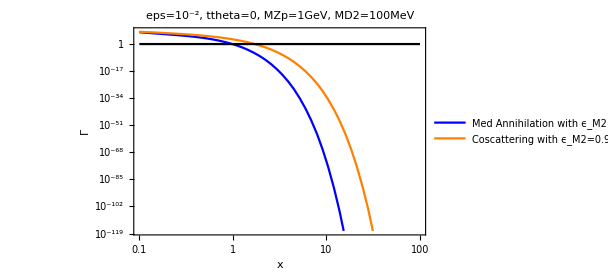

```mathematica
LogLogPlot[{Rate21[x]/(neqDM[x]*H[MD1/x])//.ModelParam1/.ModelParam-> ModelParam1,Rate31[x]/(neqDM[x]*H[MD1/x])//.ModelParam1/.ModelParam-> ModelParam1,1},{x,xval[[1]],xval[[-1]]},Frame->True,FrameLabel->{"x","Γ"},PlotLabel->Style ["eps=10^-2, ttheta=0, MZp=1GeV, MD2=100MeV",FontSize->15],LabelStyle->Larger,ImageSize->450,PlotStyle->{Blue,Orange,Black},PlotLegends->{"Med Annihilation with ϵ_M2=0.9","Coscattering with ϵ_M2=0.9"}(*,PlotRange->{{0.1,10},{10^-5,10^5}}*)]
```

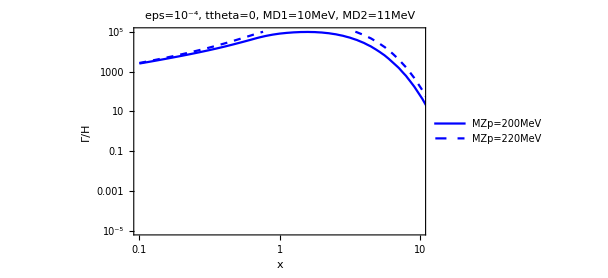

```mathematica
Get[NotebookDirectory[]<>"Coscattering.wl"];
xval=Round[10^Range[Log10[10^-1],Log10[100],0.05]*10^5]*10^-5;
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->200,MD2->MD1(1+10^-1),MD1->100};
Data21=AveragedXsec[ModelParam,2,xval];
Rate21[x_]:=If[x<Data21[[-1,1]],Exp[Interpolation[Log[Data21],Log[x],InterpolationOrder->1]],0];
ModelParam={aX->1,epsilon->10^-4,ttheta->10^(0),MZp->220,MD2->MD1(1+10^-1),MD1->100};
Data22=AveragedXsec[ModelParam,2,xval];
Rate22[x_]:=If[x<Data22[[-1,1]],Exp[Interpolation[Log[Data22],Log[x],InterpolationOrder->1]],0];
LogLogPlot[{Rate21[x]/(neqDM[x]*H[MD1/x])/.ModelParam,Rate22[x]/(neqDM[x]*H[MD1/x])/.ModelParam},{x,xval[[1]],xval[[-1]]},Frame->True,FrameLabel->{"x","Γ/H"},PlotLabel->Style ["eps=10^-4, ttheta=0, MD1=10MeV, MD2=11MeV",FontSize->15],LabelStyle->Larger,ImageSize->450,PlotStyle->{Blue,{Blue,Dashed}},PlotLegends->{"MZp=200MeV","MZp=220MeV"},PlotRange->{{0.1,10},{10^-5,10^5}}]
```

### Plotting Data

```mathematica
data={};
For[LogTanT=-5,LogTanT≤-3,LogTanT=LogTanT+1/4,
(*For[LogMZp=3,LogMZp≤7,LogMZp=LogMZp+1/4,*)
For[LogEpsM=-2,LogEpsM≤0,LogEpsM=LogEpsM+1/8,
(*ModelParam={aX->1,epsilon->10^-2,ttheta->10^LogTanT,MZp->10^LogMZp,MD1->10,MD2->MD1*(1+10^-1)};*)
ModelParam={aX->1,epsilon->10^-2,ttheta->10^LogTanT,MZp->2*10^3,MD1->10^3,MD2->MD1*(1+10^LogEpsM)};
Coscat=CalcGaScat[ModelParam,1,3];
AppendTo[data,{LogEpsM//N,LogTanT//N,CalcGaScat[ModelParam,1,3]/(neqDM[1]*H[MD1/1])/.ModelParam}];]]
Export[NotebookDirectory[]<>"EffRegion.dat",data]
```

NIntegrate::precw: The precision of the argument function ((5.71324994743819890985335250916725860247×10^-8 «4»)/((1.×10^6-1.027884146294307081965183584447556208617×10^6 y)^2)) is less than WorkingPrecision (40.).

NIntegrate::precw: The precision of the argument function ((5.738313053240893869120943933868351096912×10^-8 «4»)/((1.×10^6-1.036922251103365891748736837062911837987×10^6 y)^2)) is less than WorkingPrecision (40.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

/home/sam/OneDrive/Coscattering/EffRegion.dat

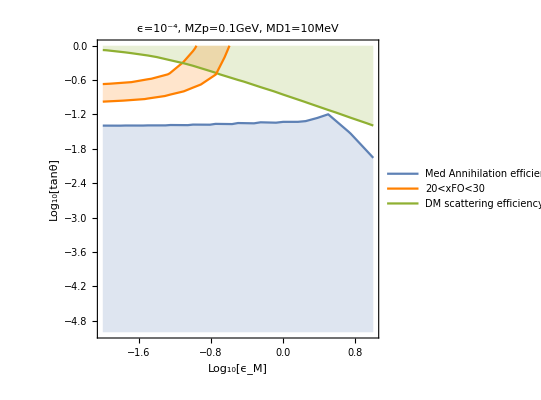

```mathematica
LogMZp=2;

data=Import[NotebookDirectory[]<>"CoscatteringRegion_Full_eps_1e-4.dat"];
data=Select[data,#[[1]]==LogMZp&];
data=DeleteCases[data,x_/;Sign[x[[4]]]==-1];
ListContourPlot[{Table[{data[[i,2]],data[[i,3]],Log10[data[[i,4]]]},{i,1,Length[data]}]},Contours->{0}];
OrderedPairs1=Cases[Normal@%,Line[pts_]->pts,Infinity][[1]];
ListContourPlot[{Table[{data[[i,2]],data[[i,3]],Log10[data[[i,8]]]},{i,1,Length[data]}]},Contours->{Log10[20],Log10[30]}];
OrderedPairs2=Cases[Normal@%,Line[pts_]->pts,Infinity];
ListContourPlot[{Table[{data[[i,2]],data[[i,3]],Log10[data[[i,7]]]},{i,1,Length[data]}]},Contours->{0}];
OrderedPairs3=Cases[Normal@%,Line[pts_]->pts,Infinity][[1]];
ListPlot[{OrderedPairs1,Append[OrderedPairs2[[1]],{OrderedPairs2[[2,1,1]],1}],OrderedPairs3,Reverse[OrderedPairs2[[2]]]},Frame->True,Joined->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"Log_10[ϵ_M]","Log_10[tanθ]"},PlotLabel->"ϵ=10^-4, MZp="<>ToString[10.^(LogMZp-3)]<>"GeV, MD1=10MeV",AxesOrigin->{3,0},PlotStyle->{Automatic,Orange,Automatic,Orange},Filling->{1->Bottom,2->{4},3->Axis},PlotRange->{{-2,1},{-5,0}},PlotLegends->{"Med Annihilation efficiency at x=xFO","20<xFO<30","DM scattering efficiency at x=xFO"}]
```

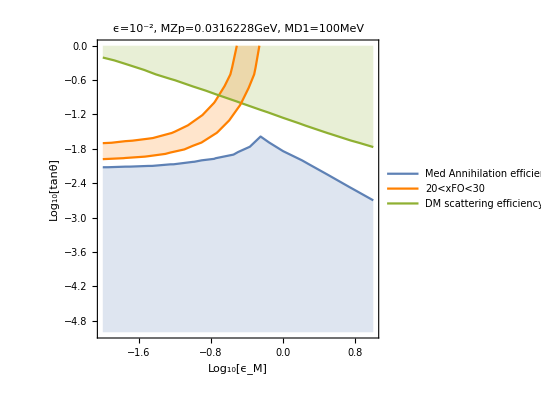

```mathematica
LogMZp=1.5;

data=Import[NotebookDirectory[]<>"CoscatteringRegion_Full_eps_1e-4.dat"];
data=Select[data,#[[1]]==LogMZp&];
data=DeleteCases[data,x_/;Sign[x[[4]]]==-1];
ListContourPlot[{Table[{data[[i,2]],data[[i,3]],Log10[data[[i,4]]]},{i,1,Length[data]}]},Contours->{0}];
OrderedPairs1=Cases[Normal@%,Line[pts_]->pts,Infinity][[1]];
ListContourPlot[{Table[{data[[i,2]],data[[i,3]],Log10[data[[i,8]]]},{i,1,Length[data]}]},Contours->{Log10[20],Log10[30]}];
OrderedPairs2=Cases[Normal@%,Line[pts_]->pts,Infinity];
ListContourPlot[{Table[{data[[i,2]],data[[i,3]],Log10[data[[i,7]]]},{i,1,Length[data]}]},Contours->{0}];
OrderedPairs3=Cases[Normal@%,Line[pts_]->pts,Infinity][[1]];
ListPlot[{OrderedPairs1,Append[OrderedPairs2[[1]],{OrderedPairs2[[2,1,1]],1}],OrderedPairs3,Reverse[OrderedPairs2[[2]]]},Frame->True,Joined->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"Log_10[ϵ_M]","Log_10[tanθ]"},PlotLabel->"ϵ=10^-2, MZp="<>ToString[10.^(LogMZp-3)]<>"GeV, MD1=100MeV",AxesOrigin->{3,0},PlotStyle->{Automatic,Orange,Automatic,Orange},Filling->{1->Bottom,2->{4},3->Axis},PlotRange->{{-2,1},{-5,0}},PlotLegends->{"Med Annihilation efficiency at x=xFO","20<xFO<30","DM scattering efficiency at x=xFO"}]
```

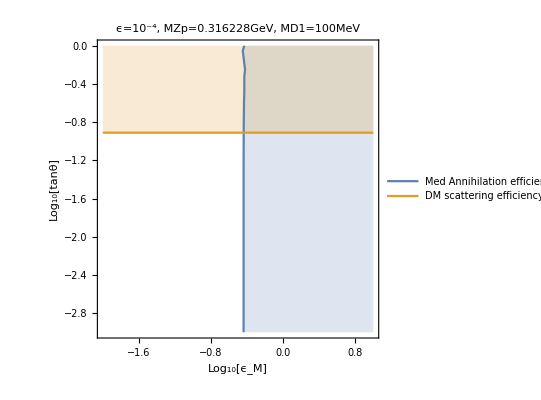

```mathematica
LogMZp=2.5;

data=Import[NotebookDirectory[]<>"CoscatteringRegion_x10.dat"];
data=Select[data,#[[1]]==LogMZp&];
data=DeleteCases[data,x_/;Sign[x[[4]]]==-1];
ListContourPlot[{Table[{data[[i,2]],data[[i,3]],Log10[data[[i,4]]]},{i,1,Length[data]}]},Contours->{0}];
OrderedPairs1=Cases[Normal@%,Line[pts_]->pts,Infinity][[1]];
ListContourPlot[{Table[{data[[i,2]],data[[i,3]],Log10[data[[i,5]]]},{i,1,Length[data]}]},Contours->{0}];
OrderedPairs2=Cases[Normal@%,Line[pts_]->pts,Infinity][[1]];
ListPlot[{Append[OrderedPairs1,{1,1}],OrderedPairs2},Frame->True,Joined->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"Log_10[ϵ_M]","Log_10[tanθ]"},PlotLabel->"ϵ=10^-4, MZp="<>ToString[10.^(LogMZp-3)]<>"GeV, MD1=100MeV",AxesOrigin->{3,0},Filling->{1->Bottom,2->Top},PlotRange->{{-2,1},{-3,0}},PlotLegends->{"Med Annihilation efficiency at x=10","DM scattering efficiency at x=10"}]
```

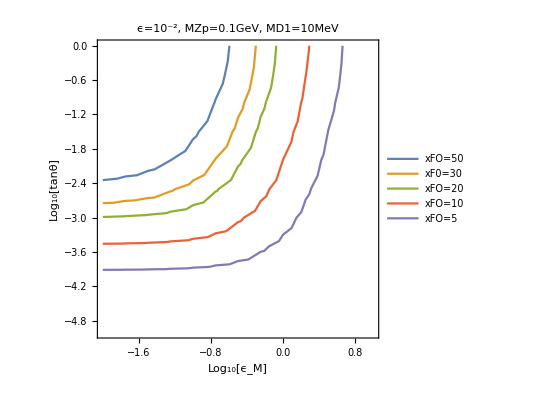

```mathematica
LogMZp=2;

data=Import[NotebookDirectory[]<>"CoscatteringRegion_Full_eps_10.dat"];
data=Select[data,#[[1]]==LogMZp&];
data=DeleteCases[data,x_/;Sign[x[[4]]]==-1];
ListContourPlot[{Table[{data[[i,2]],data[[i,3]],data[[i,8]]},{i,1,Length[data]}]},Contours->{5,10,20,30,50}];
OrderedPairs1=Cases[Normal@%,Line[pts_]->pts,Infinity];
ListPlot[OrderedPairs1,Frame->True,Joined->True,AspectRatio->1,LabelStyle->Larger,FrameLabel->{"Log_10[ϵ_M]","Log_10[tanθ]"},PlotLabel->"ϵ=10^-2, MZp="<>ToString[10.^(LogMZp-3)]<>"GeV, MD1=10MeV",AxesOrigin->{3,0},PlotRange->{{-2,1},{-5,0}},PlotLegends->{"xFO=50","xF0=30","xFO=20","xFO=10","xFO=5"}]
```

### Testing Xsec dependence on DeltaM

```mathematica
Get[NotebookDirectory[]<>"m_files/Int_symb2_Chi2Chi2_ee.m"];
Get[NotebookDirectory[]<>"Coscattering.wl"];
```

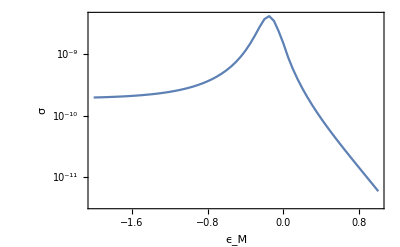

```mathematica
ModelParam={aX->1,epsilon->10^-2,ttheta->10^-5,MZp->400,MD1->10^2,MD2->MD1(1+eps)};
Table[{e,N[σ/.s->6MD2^2//.Relations//.SMMasses//.ModelParam/.eps->10^e,20]},{e,-2,1,5*10^-2}];
ListLogPlot[%,Frame->True,Joined->True,FrameLabel->{"ϵ_M","σ"},LabelStyle->Larger]
```

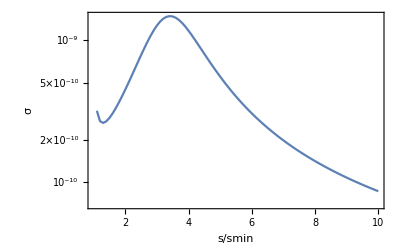

```mathematica
ModelParam={aX->1,epsilon->10^-2,ttheta->10^-5,MZp->400,MD1->10^2,MD2->MD1(1+10^(-1))};
Table[{y,N[σ/.s->y *4*MD2^2//.Relations//.SMMasses//.ModelParam,20]},{y,11/10,10,10^-1}];
ListLogPlot[%,Frame->True,Joined->True,FrameLabel->{"s/smin","σ"},LabelStyle->Larger,PlotRange->{{1,10},All}]
```

```mathematica
MZp/.ModelParam//N
MD2//.ModelParam/.eps->1
```

400.

200